# Notes (MATH152, 2017-11-06)

## Section 10.2

```mathematica
x=f(t), y=g(t), a≤t≤b
ⅆy/ⅆt=ⅆy/ⅆx·ⅆx/ⅆt
ⅆy/ⅆx=(ⅆy/ⅆt)/(ⅆx/ⅆt)=(g'(t))/(f'(t)) (if f'(t)≠0)
```

If ⅆy/ⅆt=0 and ⅆx/ⅆt≠0, ⅆy/ⅆx=0: the tangent is horizontal.
If ⅆx/ⅆt=0 and ⅆy/ⅆt≠0: the tangent is vertical.

```mathematica
(ⅆ^2 y)/(ⅆ x^2)=ⅆ/ⅆx(ⅆy/ⅆx)=(ⅆ/ⅆt(ⅆy/ⅆx))/(ⅆx/ⅆt)=(g''(t)f'(t)-g'(t)f''(t))/[f'(t)]^3
```

```mathematica
x=t^2, y=t^3-3t
x-intercepts: 0=t^3-3t=t(t^2-3)⟹t=0, ±√3⟹x=0,3
```

```mathematica
ⅆy/ⅆx=(3(t^2-1))/(2t)
t=±√3⟹ⅆy/ⅆx=±√3
t=0⟹ⅆy/ⅆx=-∞
```

```mathematica
horizontal when 3(t^2-1)=0, i.e. ±1:
t=±1⟹ⅆy/ⅆx=0, x=1, y= ∓2
```

```mathematica
(ⅆ^2 y)/(ⅆ x^2)=(ⅆ/ⅆt(ⅆy/ⅆx))/(ⅆx/ⅆt)=(ⅆ/ⅆt[3/2(t-1/t)])/(2t)=(3 t^2+1)/(4 t^3)
3 t^2+1≥1⟹3 t^2+1>0, ∴ concavity depends only on 4 t^3;
Concave down: 4 t^3<0⟹t<0
Concave up: 4 t^3>0⟹t>0
```

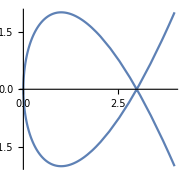

```mathematica
ParametricPlot[{x=t^2,y=t^3-3t},{t,-2,+2}]
```

```mathematica
y=F(x)≥0, the area under the curve described by F(x) from x=a to x=b is:
A=∫_a^b F(x)ⅆx
```

```mathematica
If x=f(t), y=g(t), Subscript[S, 1]≤t≤Subscript[S, 2] traces the same curve once,'
A=∫yⅆx=∫_Subscript[S, 1]^Subscript[S, 2] g(t)f'(t)ⅆt if f(a)=Subscript[S, 1], f(b)=Subscript[S, 2]
or ∫_Subscript[S, 2]^Subscript[S, 1] g(t)f'(t)ⅆt if f(a)=Subscript[S, 2], f(b)=Subscript[S, 1]
```

```mathematica
θ=π/3
x=r(θ-sin θ), y=r(1-cos θ), 0≤θ≤2π, 0≤x≤2πr
```

```mathematica
A=∫_0^(2πr) yⅆx=∫_0^(2π) [r(1-cos θ)][r(1-cos θ)]ⅆx=∫_0^(2π) (r^2(1-cos θ))^2 ⅆx=r^2∫_0^(2π) 1-2cos θ+cos^2 θⅆx=r^2∫_0^(2π) 1-2cos θ+1/2(1+cos 2θ)ⅆx=Subscript[(r^2)[3/2 θ-2sin θ+1/4 sin 2θ], 0]^(2π)=(r^2)[3/2 2π]=3 πr^2
```

pg. 692, 693: full derivation of arc-lengths on parametric equations, but:

```mathematica
L=∫ⅆs=∫√(1+(ⅆy/ⅆx)^2)ⅆx=∫√((ⅆx)^2+(ⅆy)^2)ⅆx
=∫√((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt
L=∫_Subscript[S, 2]^Subscript[S, 2] [f'(t)]2+[g'(t)]^2 ⅆt
```

```mathematica
x=r cos t, y=r sin t, 0≤t≤2π
```

```mathematica
L=∫_0^(2π) √(r^2 sin^2 t+r^2 cos^2 t)ⅆt=r∫_0^(2π) √(sin^2 t+cos^2 t)ⅆt=r∫_0^(2π) √1 ⅆt=[r·t]_0^(2π)=2πr
```

Length of arch of cycloid:

```mathematica
L=∫_0^(2π) √((r^2(1-cos θ))^2+r^2 sin^2 θ)ⅆθ=r∫_0^(2π) √((1-cos θ)^2+sin^2 θ)ⅆθ=r|_0^(2π)∫_0^(2π) √((1-cos θ)^2+sin^2 θ)ⅆθ=r|_0^(2π)∫_0^(2π) √(1-2cos θ+cos^2 θ+sin^2 θ)ⅆθ=r|_0^(2π)∫_0^(2π) √(2(1-cos θ))ⅆθ=…
1/2(1-cos 2x)=sin^2 x⟹^(θ=2x)1/2(1-cos θ)=sin^2 θ/2⟹2(1-cos θ)=4 sin^2(θ/2)
…=r|_0^(2π)∫_0^(2π) √(4 sin^2(θ/2))ⅆθ=r|_0^(2π)∫_0^(2π) 2sin(θ/2)ⅆθ=^…8r
```

Sec. 8.2 summary:

```mathematica
S=∫_a^b 2π F(x)√(1+[F'(x)]^2)ⅆx=∫_a^b 2π y √(1+[ⅆy/ⅆx]^2)ⅆx=∫_a^b 2π y ⅆs=∫_a^b 2π g(t)√([f'(t)]^2+[g'(t)]^2)ⅆt
```

Surface area of a sphere, radius r:

```mathematica
x=r cos θ, y=r sin θ, 0≤t≤π
```

```mathematica
S=∫_0^π 2π r sin t √(r^2 sin^2 t+r^2 cos^2 t)ⅆt=[2 πr^2(-cos t)]_0^π=2 πr^2(1+1)=4 πr^2
```